```mathematica
PRÀCTICA 7:APROXIMACIÓ NUMÈRICA DE SOLUCIONS D'EQUACIONS
```

```mathematica
En primer lloc, copiem (de FuncionsPredefinides.nb) i executem les funcions que permeten aplicar els mètodes de la Bisecció i de Newton:
```

```mathematica
Biseccio[f_,{a_,b_,M_}]:=Module[{an,bn,xn},
an=a;
bn=b;
For[i=1,i≤M,i++,
xn=(an+bn)/2;
If[f[xn]==0,Break[],
If[f[an]*f[xn]<0, bn=xn,
If[f[xn]*f[bn]<0,an=xn]
]
]
];
N[xn,20]
]
```

```mathematica
Newton[f_,x0_,M_]:=Module[{xn},
xn=x0;
For[i=1, i≤M, i++,
xn=xn-f[xn]/f'[xn]
];
N[xn,20]
]
```

```mathematica
ACTIVITAT 1
```

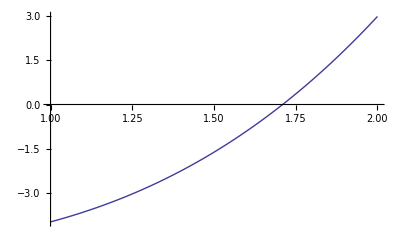

```mathematica
Plot[x^3-5,{x,1,2}]
```

```mathematica
La funció x^3-5 és contínua i té només una arrel dins de l'interval [1,2]. Podem aplicar, per tant, el mètode de la Bisecció a aquest interval. Com volem 10 xifres decimals exactes, hem d'imposar la condició de que l'error siga <(10^-11). Tenint en compte la cota de l'error que apareix en el butlletí, imposarem la condició
(b-a)/2^n<(10^-11). Aïllant n s'obté:( b-a)10^11<2^n⟹ Log[2^n]>Log[( b-a)10^11]⟹ n Log[2]>Log[( b-a)10^11] ⟹ n>Log[( b-a)10^11]/Log[2]
En el nostre cas, a=1 i b=2.
```

```mathematica
N[Log[10^11]/Log[2]]
```

36.5412

```mathematica
Per tant, necessitarem 37 iteracions del mètode de la Bisecció.
```

```mathematica
f[x_]=x^3-5
```

-5+x^3

```mathematica
Biseccio[f,{1,2,37}]
```

1.7099759466727846302

```mathematica
L'aproximació obtinguda amb 10 xifres decimals correctes és: 1.7099759466
```

```mathematica
N[5^(1/3),12]
```

1.70997594668

```mathematica
Com podem comprovar, 10 xifres decimals correctes queden garantides.
```

```mathematica
ACTIVITAT 2
```

```mathematica
F[x_]=x^2-Cos[x]+Sin[x]
```

x^2-Cos[x]+Sin[x]

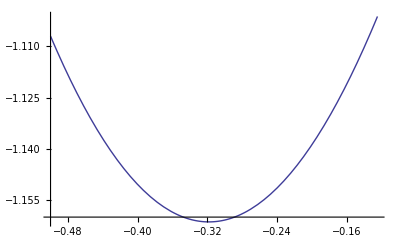

```mathematica
Plot[F[x],{x,-0.5,-0.125}]
```

```mathematica
L'abcissa d'aquest mínim relatiu ha d'anul·lar a la primera derivada de F. Per tant, hem de resoldre l'equació F'(x)=0 a l'interval [-0.5,-0.125] aplicant el mètode de la Bisecció. Igual que abans, si volem 10 xifres decimals exactes hem d'imposar la condició (b-a)/2^n<(10^-11).  Aïllant igual que abans: n>(Log[( b-a)10^11]/Log[2]). En aquest cas  a=-0.5 i b=-0.125.
```

```mathematica
N[Log[( -0.125-(-0.5))10^11]/Log[2]]
```

35.1262

```mathematica
Necessitarem, per tant, 36 iteracions:
```

```mathematica
Biseccio[F',{-0.5,-0.125,36}]
```

-0.318366

```mathematica
L'aproximació obtinguda és -0.3183660000
```

```mathematica
(OBSERVACIÓ IMPORTANT: El primer input ha de ser una FUNCIÓ. Per tant, hem de posar F' i no F'[x] (que és la funció avaluada en x) )
```

```mathematica
ACTIVITAT 3
```

```mathematica
f[x_]=3x-x^3+4
```

4+3 x-x^3

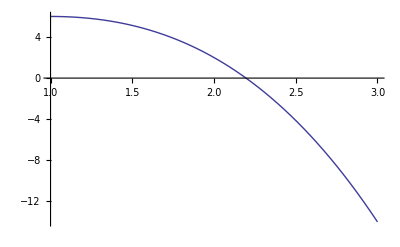

```mathematica
Plot[f[x],{x,1,3}]
```

```mathematica
Agafarem 2com a valor inicial del mètode de Newton
```

```mathematica
Newton[f,2,4]
```

2.1958233454456516143

```mathematica
L'aproximació obtinguda és 2.1958233454456516143
```

```mathematica
NSolve[f[x]==0,x,WorkingPrecision->20]
```

{{x→-1.0979116727228235764-0.7850032632435902184 ⅈ},{x→-1.0979116727228235764+0.7850032632435902184 ⅈ},{x→2.1958233454456471528}}

```mathematica
Veiem que una proximació a l'unica solució real és 2.1958233454456471528. Comparant, veiem que s'obtenen 13 xifres decimals exactes amb el mètode de Newton (i 4 iteracions).
```

```mathematica
ACTIVITAT 4
```

```mathematica
A l'activitat 2 hem obtingut que una aproximació a la solució amb 10 xifres decimals exactes és: -0.3183660000
```

```mathematica
Newton[F',-0.5,1]
```

-0.32072

```mathematica
Newton[F',-0.5,2]
```

-0.318367

```mathematica
Newton[F',-0.5,3]
```

-0.318366

```mathematica
Com veiem, només es necessiten 3 iteracions per a obtindre una precisió de 10 xifres amb el mètode de Newton. Amb el mètode de la Bisecció necessitàvem 36 iteracions.
```